# Rania — PS3 — (01-24-2025)

## Section 9 Problems

```mathematica
(*9.1 manipulate to show Range[n] with n varying from 0 to 100*)
Manipulate[Range[n], {n,0,100,1}]
(*9.2 Manipulate to plot the whole numbers up to n, where n ranges from 5 to 50*)
Manipulate[ListPlot[Range[n]], {n,5,50,1}]
(*9.3 Manipulate to show a column of between 1 and 10 copies of x*)
Manipulate[Column[Table[x,n]],{n,1,10,1}] (*note to Rania, use two variables: "x" to display output, and "n" to indicate the copies i.e manipulated number*)
(*9.4 Manipulate to show a disk with a hue varying from 0 to 1 *)
Manipulate[Graphics[Style[Disk[],Hue[h]]], {h,0,1,.01}]
(*9.5 Manipulate to show a disk with red, green and blue color components varying from 0 to 1. *)
Manipulate[Graphics[Style[Disk[],Blend[{RGBColor[r,0,0], RGBColor[0,g,0], RGBColor[0,0,b]}]]], {r, 0, 1, .01} ,{g, 0, 1, .01} , {b, 0, 1, .01} ] 
(*9.6 Manipulate to show digit sequences of 4-digit integers (between 1000 and 9999) *)
Manipulate[IntegerDigits[n], {n,1000,9999,1}]
(*9.7 Manipulate to create a list of between 5 and 50 equally spaced hues*)
Manipulate[Table[Hue[h], {h, 0, 1, 1/(n - 1)}], {n, 5, 50, 1}] (*DAMN HARD- There's gotta be a better way*)
(*9.8 Manipulate that shows a list of a variable number of hexagons (between 1 and 10), and with variable hues*)
Manipulate[Table[Graphics[Style[RegularPolygon [6],Hue[h]]],n], {h,0,1,0.1}, {n,1,10,1}] (*Sorta slow to load!*)
(*9.9  Manipulate that lets you show a regular polygon with between 5 and 20 sides, in red, yellow or blue *)
Manipulate[Graphics[Style[RegularPolygon[s], color]], {s,5,20,1}, {color,{Red, Yellow, Blue}}]
(*9.10  Manipulate that shows a pie chart with a number of equal segments varying from 1 to 10 *)
Manipulate[PieChart[Table[n,n]], {n,1,10,1}]
(*9.11  Manipulate that gives a bar chart of the 3 digits in integers from 100 to 999 *)
Manipulate[BarChart[IntegerDigits[n]], {n,100,999,1}]
(*9.12 Manipulate that shows n random colors, where n can rane from 1 to 50*)
Manipulate[Table[RandomColor[], n], {n,1,50,1}]
(*9.13 Manipulate to display a column of integer powers with bases from 1 to 25 and exponents from 1 to 10*)
Manipulate[Column[Table[n^p, {p,Range[p]}]], {n,1,25,1},{p,1,10,1}]
(*9.14 Manipulate of a number line of values of x^n for integer x from 1 to 10, with n varying from 0 to 5 *)
Manipulate[NumberLinePlot[Table[x^n, {x, Range[10]}]],{n,0,5,1}]
(*9.15 Show a sphere that can vary in color green to red*)
Manipulate[Graphics3D[Style[Sphere[],RGBColor[g,255-g,0]]], {g,0,1,.1}]
```

## Section 10 Problems

```mathematica
photoRef = -Graphics-
```

-Graphics-

```mathematica
(*10.1 Color negate the result of edge decting an image *)
ColorNegate[EdgeDetect[photoRef]]
(*10.2 Manipulate to make an interface for blurring an image from 0 to 20 *)
Manipulate[Blur[photoRef, n], {n,0,20,1}]
(*10.3 Make a table of results from edge an image with blurring from 1 to 10*)
Table[EdgeDetect[Blur[photoRef, n]], {n,1,10}]
(*10.4 Make an image collage of an image together with the results of blurring, edge decting, and binarizing it *)
ImageCollage[{photoRef, Blur[photoRef], EdgeDetect[photoRef], Binarize[photoRef]}]
(*10.5 Add an image to a binarized version of it *)
ImageAdd[photoRef, Binarize[photoRef]]
(*10.6 Manipulate to display edges of an image as it gets blurred from 0 to 20*)
Manipulate[EdgeDetect[Blur[photoRef], n],{n,0,20,1}]
(*10.7 Edge Detect a picture of a sphere *)
EdgeDetect[Graphics3D[Sphere[]]]
(*10.8 Manipulate to make an interface for blurring a pentagon from 0 to 20*)
Manipulate[ Blur[Graphics[RegularPolygon[5]], n], {n,0,20,1}]
(*10.9 Collage of 9 images of disks, each with a random color *)
ImageCollage[Table[Graphics[Style[Disk[],RandomColor[]]],9]]
(*10.10 Use ImageCollage to make a combined image of spheres with hues from 0 to 1 in steps of 0.2 *)
ImageCollage[Table[Graphics3D[Style[Sphere[], Hue[n]]], {n,0,1,0.2}]]
(*10.11 Table of blurring a disk by an amount from 0 to 30 in steps of 5*)
Table[Blur[Graphics[Disk[]],n],{n,0,30,5}]
(*10.12 Add an image to an image of a disk*)
ImageAdd[{photoRef,Graphics[Disk[]]}]
(*10.13 Add an image to an image of a red octagon*)
ImageAdd[{photoRef,Graphics[Style[RegularPolygon[8],Red]]}]
(*10.14 Add an image to the color negated version of the edge detected image*)
ImageAdd[{photoRef, ColorNegate[EdgeDetect[photoRef]]}]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

-Graphics-

-Graphics-

## Section 11 Problems

JoinJoin

ABCDEFGHIJKLMNOPQRSTUVWXYZ

zyxwvutsrqponmlkjihgfedcba

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

abcdef

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings

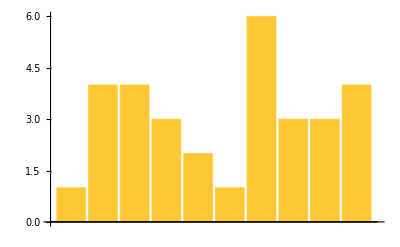

60266

9271

{String or strings may refer to:}

AMTTACCESEMTTTCTPP=ITTDBTTTT==DTLTTTSITIIDMTTAAATTTIASIBIAITITIITSI=CCAHTFTTTAEBNH=ITax()2{,THI=DHTTTTAB==CBTDETTITIRTZTT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAATBAIL=TJFCJTHATHTTWITT=TTDTKIHKNNHPNIMTGFTTWISTITS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCICW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETHOBSA=CTITTITCITA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M

{23}

194

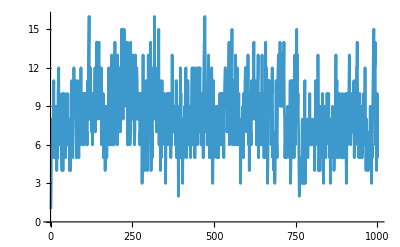

WordCloud::nomem: Not enough memory available to compute the word cloud.

```mathematica
(*11.1 Join two copies of the string "Hello"*)
StringJoin["Join", "Join"]
(*11.2 A single string of the whole alphabet in uppercase*)
ToUpperCase[StringJoin[Alphabet[]]]
(*11.3 A string of the alphabet in reverse order*)
StringReverse[StringJoin[Alphabet[]]]
(*11.4 Join 100 copies of "AGCT"*)
StringJoin[Table["AGCT",100]]
(*11.5 Use StringTake, StringJoin, and Alphabet to get "abcdef"*)
StringTake[StringJoin[Alphabet[]], 6]
(*11.6 Column with increasing numbers of letters from the string "this is about strings"*)
Column[Table[StringTake["this is about strings",n],{n,1,StringLength["this is about strings"]}]]
(*11.7 Bar chart of the lengths of the words in “A long time ago,in a galaxy far,far away”*)
BarChart[StringLength[TextWords["A long time ago,in a galaxy far,far away"]]]
(*11.8 String length of Wikipedia article for "computer"*)
StringLength[WikipediaData["computer"]]
(*11.9 Number of words in that same article*)
Length[TextWords[WikipediaData["computer"]]]
(*11.10 First sentence in the Wiki article about "strings"*)
Take[TextSentences[WikipediaData["strings"]],1]
(*11.11 String from the first letters of all sentences in the Wikipedia rticle about computers *)
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
(*11.12 Find the maximum word length among English words from WordList[]*)
Take[Reverse[Sort[StringLength[WordList[]]]],1]
(*11.13 The number of words in WordList[] that start with “q”*)
Count[StringTake[WordList[],1],"q"]
(*11.14 A line plot of the lengths of the first 1000 words from WordList[]*)
ListLinePlot[StringLength[Take[WordList[],1000]]]
(*11.15 Using StringJoin and Characters to make a word cloud of all letters in the words from WordList[]*)
WordCloud[StringJoin[Characters[WordList[]]]] (*Not enough memory but checking it in the cloud says it's correct*)
```